```mathematica
dateMouseSessionListV1={{"030921","Mouse23324","Session4"},{"031621","Mouse23324","Session2"},{"032021","Mouse23324","Session4"},{"030821","Mouse23321","Session1"},{"031121","Mouse23321","Session2"},{"031621","Mouse23321","Session2"},{"031921","Mouse23321","Session2"},{"010621","Mouse23332","Session1"},{"010821","Mouse23332","Session2"},{"011321","Mouse23332","Session1"},{"011821","Mouse23332","Session1"},{"010921","Mouse23305","Session2"},{"011121","Mouse23305","Session2"},{"121020","Mouse23312","Session4"},{"121420","Mouse23312","Session2"}};
```

```mathematica
dateMouseSessionListV2m={{"030221","Mouse23310","Session1"},{"021721","Mouse23338","Session1"},{"030221","Mouse23338","Session1"},{"031621","Mouse23338","Session1"},{"031821","Mouse23338","Session2"},{"011721","Mouse23390","Session2"},{"011821","Mouse23390","Session2"},{"022821","Mouse23390","Session1"},{"021221","Mouse23359","Session2"},{"010321","Mouse23382","Session1"},{"010621","Mouse23382","Session2"}};
```

```mathematica
(**********************************************)
(*******Generate plots in Figure S3F****************) 
(**********************************************)
```

```mathematica
meanDFFpupilCCV1=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V1/ValuesForPlotting/meanDFFpupilCrossCorr_V1.txt","List"];
```

```mathematica
semDFFpupilCCV1=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V1/ValuesForPlotting/semDFFpupilCrossCorr_V1.txt","List"];
```

```mathematica
(*********)
```

```mathematica
meanDFFpupilCCV2m=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V2m/ValuesForPlotting/meanDFFpupilCrossCorr_V2m.txt","List"];
```

```mathematica
semDFFpupilCCV2m=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V2m/ValuesForPlotting/semDFFpupilCrossCorr_V2m.txt","List"];
```

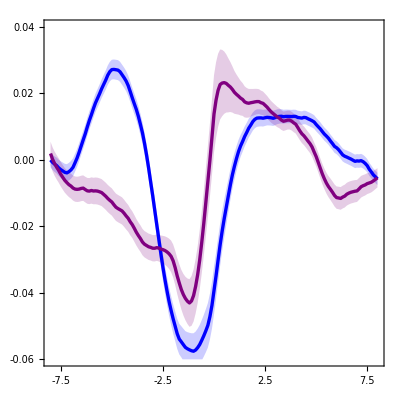

```mathematica
ListLinePlot[{Part[#,2]&/@meanDFFpupilCCV1,Part[#,2]&/@meanDFFpupilCCV1+(Part[#,2]&/@semDFFpupilCCV1),Part[#,2]&/@meanDFFpupilCCV1-(Part[#,2]&/@semDFFpupilCCV1),Part[#,2]&/@meanDFFpupilCCV2m,Part[#,2]&/@meanDFFpupilCCV2m+(Part[#,2]&/@semDFFpupilCCV2m),Part[#,2]&/@meanDFFpupilCCV2m-(Part[#,2]&/@semDFFpupilCCV2m)},Filling->{1->{{2},Directive[Opacity[0.2],Blue]},1->{{3},Directive[Opacity[0.2],Blue]},4->{{5},Directive[Opacity[0.2],Purple]},4->{{6},Directive[Opacity[0.2],Purple]}},PlotStyle->{{Blue,Thickness[0.006]},Transparent,Transparent,{Purple,Thickness[0.006]},Transparent,Transparent,{Darker@Orange,Thickness[0.006]},Transparent,Transparent,{Darker@Yellow,Thickness[0.006]},Transparent,Transparent},DataRange->{-8,8},PlotRange->{{-8,8},{-0.06,0.04}},FrameTicks->{{LinTicks[-0.06,0.04,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-8,8,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

```mathematica
(**********************************************)
(*******Generate plots in Figure S3G****************) 
(**********************************************)
```

```mathematica
meanDFFpupilPhaseV1=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V1/ValuesForPlotting/meanDFFpupilPhase_V1.txt","List"];
```

```mathematica
semDFFpupilPhaseV1=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V1/ValuesForPlotting/semDFFpupilPhase_V1.txt","List"];
```

```mathematica
meanDFFpupilPhaseV2m=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V2m/ValuesForPlotting/meanDFFpupilPhase_V2m.txt","List"];
```

```mathematica
semDFFpupilPhaseV2m=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V2m/ValuesForPlotting/semDFFpupilPhase_V2m.txt","List"];
```

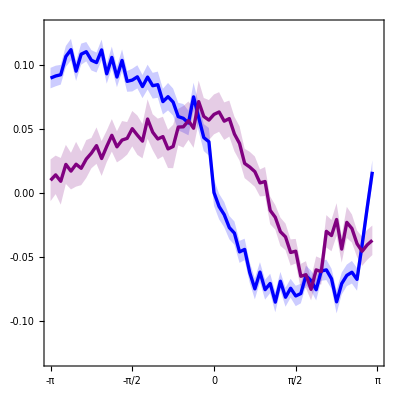

```mathematica
ListLinePlot[{Part[#,2]&/@meanDFFpupilPhaseV1,Part[#,2]&/@meanDFFpupilPhaseV1+(Part[#,2]&/@semDFFpupilPhaseV1),Part[#,2]&/@meanDFFpupilPhaseV1-(Part[#,2]&/@semDFFpupilPhaseV1),Part[#,2]&/@meanDFFpupilPhaseV2m,Part[#,2]&/@meanDFFpupilPhaseV2m+(Part[#,2]&/@semDFFpupilPhaseV2m),Part[#,2]&/@meanDFFpupilPhaseV2m-(Part[#,2]&/@semDFFpupilPhaseV2m)},Filling->{1->{{2},Directive[Opacity[0.2],Blue]},1->{{3},Directive[Opacity[0.2],Blue]},4->{{5},Directive[Opacity[0.2],Purple]},4->{{6},Directive[Opacity[0.2],Purple]}},PlotStyle->{{Blue,Thickness[0.006]},Transparent,Transparent,{Purple,Thickness[0.006]},Transparent,Transparent},DataRange->{-π,(31 π)/32},PlotRange->{{-π,π},{-0.13,0.13}},FrameTicks->{{LinTicks[-0.13,0.13,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-π,π,π/2,4,TickLabelFunction->(Rationalize[#/π]*π&),MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

```mathematica
(**********************************************)
(*******Generate plots in Figure S3H****************) 
(**********************************************)
```

```mathematica
peakCCValsV1=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V1/ValuesForPlotting/peakDFFpupilCC_V1.txt","List"];
```

```mathematica
peakCCValsV2m=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V2m/ValuesForPlotting/peakDFFpupilCC_V2m.txt","List"];
```

```mathematica
v1Charts=Show[BoxWhiskerChart[peakCCValsV1,{{"Whiskers", Directive[Blue,Thick]}, {"Fences", Directive[Blue,Thick]},{"MedianMarker", Directive[Blue,Thickness[0.009]]}},PlotRange->{All,{0,0.7}},ChartStyle->Directive[Blue,Opacity[0.3]],Frame->False],DistributionChart[peakCCValsV1,PlotRange->{All,{0,0.7}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Blue],Frame->False],FrameTicks->{{LinTicks[0,0.7,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
pmCharts=Show[BoxWhiskerChart[peakCCValsV2m,{{"Whiskers", Directive[Purple,Thick]}, {"Fences", Directive[Purple,Thick]},{"MedianMarker", Directive[Purple,Thickness[0.009]]}},PlotRange->{All,{0,0.7}},ChartStyle->Directive[Purple,Opacity[0.3]],Frame->False],DistributionChart[peakCCValsV2m,PlotRange->{All,{0,0.7}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Purple],Frame->False],FrameTicks->{{LinTicks[0,0.7,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
transp=Show[BoxWhiskerChart[peakCCValsV2m,{{"Whiskers", Directive[Transparent,Thick]}, {"Fences", Directive[Transparent,Thick]},{"MedianMarker", Directive[Transparent,Thickness[0.009]]}},PlotRange->{All,{0,0.7}},ChartStyle->Transparent,Frame->False],DistributionChart[peakCCValsV2m,PlotRange->{All,{0,0.7}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Transparent],Frame->False],FrameTicks->{{LinTicks[0,0.7,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Black,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

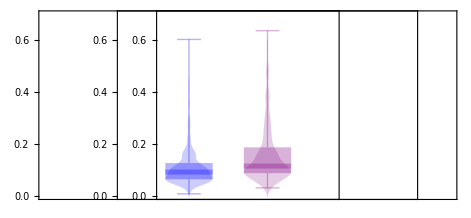

```mathematica
GraphicsRow[{v1Charts,pmCharts,transp},Spacings->{{-280,-280,-320}}]
```